## Mutual information rates (Problem 15.18)

```mathematica
Clear["Global`*"];
```

```mathematica
a[u_]:=Integrate[1/(√(2π σ^2))Exp[-x^2/(2 σ^2)],{x,u,∞},Assumptions->σ>0]
```

```mathematica
a[u]
```

1/2 Erfc[u/(√2 σ)]

```mathematica
p[y0_,u_]:=Piecewise[{{a[u](DiracDelta[y0+u]+DiracDelta[y0-u])+1/(√(2π σ^2))Exp[-y0^2/(2 σ^2)],-u<y0<u}}]
```

Now we look at the case with measurement noise of magnitude ξ

```mathematica
p0=Integrate[1/(√(2 π) ξ)Exp[-x^2/(2 ξ^2)]Piecewise[{{1/(√(2 π σ^2))Exp[-(y-x)^2/(2 σ^2)],-u<y-x<u}}],{x,-∞,∞},Assumptions->{ξ>0,σ>0}]//FullSimplify
```

Piecewise[{{(ⅇ^(-y^2/(2 (ξ^2+σ^2))) (Erf[(u ξ^2+(u+y) σ^2)/(√2 ξ σ √(ξ^2+σ^2))]-Erf[(y σ^2-u (ξ^2+σ^2))/(√2 ξ σ √(ξ^2+σ^2))]))/(2 √(2 π) √(ξ^2+σ^2)), u>0}, {0, True}}]

```mathematica
pym = a[u]/(√(2π ξ^2))(Exp[-(y-u)^2/(2 ξ^2)]+Exp[-(y+u)^2/(2 ξ^2)])+p0;
```

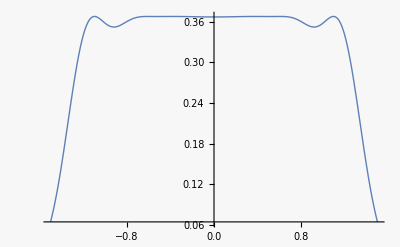

```mathematica
p1=Plot3D[pym/.{ξ->0.2,σ->1},{y,-5,5},{u,0,2},PlotRange->All];
p2=Plot[-pym Log[pym]/.{ξ->0.2,u->1,σ->1},{y,-1.5,1.5},PlotRange->All];
GraphicsRow[{p1,p2}]
```

```mathematica
h=NIntegrate[-pym Log[pym]/.{ξ->0.2,u->1,σ->1},{y,-∞,∞}]//Chop
```

1.00598

Explore continuous saturation function

Power::infy: Infinite expression 1/0 encountered.

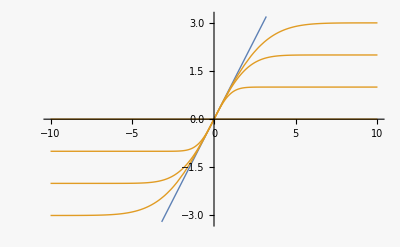

```mathematica
g[u0_,u_]:=u0 Erf[(√π u)/(2u0)]
Plot[{u,g[u0,u]/.u0->{0,1,2,3}},{u,-10,10},PlotRange->{-3.2,3.2}]
```

```mathematica
{dgdu=D[g[u0,u], u],dgdu/.u->0}
```

{ⅇ^(-(π u^2)/(4 u0^2)),1}

```mathematica
Py0=Piecewise[{{1/(√(2π))Exp[-(2/π u0^2-1)(InverseErf[y0/u0])^2],-u0<y0<u0}},y0]
```

Piecewise[{{(ⅇ^((1-(2 u0^2)/π) InverseErf[y0/u0]^2))/(√(2 π)), -u0<y0<u0}, {y0, True}}]

```mathematica
Integrate[Py0,{y0,-u0,u0},Assumptions->u0>0]
```

1

As this is complicated (and qualitatively the same),  I decided to drop it for the book.